# Source Code

## Radical pairs may explain Reactive Oxygen Species-mediated effects of hypomagnetic field on neurogenesis

## Rishabh, Hadi Zadeh-Haghighi, Christoph Simon

This code is based on source code for “Upper bound on the biological effects of 50/60 Hz magnetic fields mediated by radical pairs” by PJ Hore  https://doi.org/10.7554/eLife.44179.011

```mathematica
Id[d_]:=IdentityMatrix[d];γe=1.76086 10^8;

σ={{1/2.({{0, 1}, {1, 0}}),1/2.({{0, -ⅈ}, {ⅈ, 0}}),1/2.({{1, 0}, {0, -1}})},{1/(√2.)({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),1/(√2.)({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}}),({{1., 0, 0}, {0, 0, 0}, {0, 0, -1.}})},{1/2({{0, √3, 0, 0}, {√3, 0, 2, 0}, {0, 2, 0, √3}, {0, 0, √3, 0}}),1/2({{0, -ⅈ √3, 0, 0}, {ⅈ √3, 0, -ⅈ 2, 0}, {0, ⅈ 2, 0, -ⅈ √3}, {0, 0, ⅈ √3, 0}}),({{3/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -3/2}})},{1/2({{0, 2, 0, 0, 0}, {2, 0, √6, 0, 0}, {0, √6, 0, √6, 0}, {0, 0, √6, 0, 2}, {0, 0, 0, 2, 0}}),1/2({{0, -ⅈ 2, 0, 0, 0}, {ⅈ 2, 0, -ⅈ √6, 0, 0}, {0, ⅈ √6, 0, -ⅈ √6, 0}, {0, 0, ⅈ √6, 0, -ⅈ 2}, {0, 0, 0, ⅈ 2, 0}}),({{2, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, -1, 0}, {0, 0, 0, 0, -2}})},{1/2({{0, √5, 0, 0, 0, 0}, {√5, 0, √8, 0, 0, 0}, {0, √8, 0, √9, 0, 0}, {0, 0, √9, 0, √8, 0}, {0, 0, 0, √8, 0, √5}, {0, 0, 0, 0, √5, 0}}),1/2({{0, -ⅈ √5, 0, 0, 0, 0}, {ⅈ √5, 0, -ⅈ √8, 0, 0, 0}, {0, ⅈ √8, 0, -ⅈ √9, 0, 0}, {0, 0, ⅈ √9, 0, -ⅈ √8, 0}, {0, 0, 0, ⅈ √8, 0, -ⅈ √5}, {0, 0, 0, 0, ⅈ √5, 0}}),({{5/2, 0, 0, 0, 0, 0}, {0, 3/2, 0, 0, 0, 0}, {0, 0, 1/2, 0, 0, 0}, {0, 0, 0, -1/2, 0, 0}, {0, 0, 0, 0, -3/2, 0}, {0, 0, 0, 0, 0, -5/2}})}};

M1_⊗M2_:=KroneckerProduct[M1,M2]; M1_⊗M2_⊗M3_:=(M1⊗M2)⊗M3;

HyperfineHamiltonian[n_,spin_,hfc_]:=(
If[n==0,M=1; 
S=Table[σ[[1,p]],{p,3}]; Table[0,{2},{2}],
M=Product[spin[[k]],{k,1,n}]; II=Table[(Id[Product[spin[[k]],{k,1,j-1}]])⊗σ[[spin[[j]]-1,p]]⊗(Id[Product[spin[[k]],{k,j+1,n}]]),{j,n},{p,3}];
S=Table[σ[[1,p]]⊗Id[M],{p,3}];
Sum[hfc[[j,p,q]] σ[[1,p]]⊗II[[j,q]],{j,n},{p,3},{q,3}]  ]
);

ZeemanHamiltonian[ω0_,θ0_,ϕ0_]:=(
ω0(S[[1]] Sin[θ0]Cos[ϕ0]+S[[2]] Sin[θ0]Sin[ϕ0]+S[[3]] Cos[θ0])
);

SingletBornTripletYield[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,rate_,θ0_,ϕ0_,relax_]:=(
GG[f_,k_,R_]:=k(k+R)/((k+R)^2+f^2);
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB;
{e,v}=Eigensystem[H];v=Orthogonalize[v];
gg=Table[GG[e[[r]]-e[[s]],rate,relax],{r,4 M},{s,4 M}];
PS=Conjugate[v].(0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]]).Transpose[v];
1-(Total[PS Transpose[PS] gg,2]/(M) +(relax )/(4*(rate+relax)))//Chop  
);
TripletBornTripletYield[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,rate_,θ0_,ϕ0_,relax_]:=(
GG[f_,k_,R_]:=k(k+R)/((k+R)^2+f^2);
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB;
{e,v}=Eigensystem[H];v=Orthogonalize[v];
gg=Table[GG[e[[r]]-e[[s]],rate,relax],{r,4 M},{s,4 M}];
PS=Conjugate[v].(0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]]).Transpose[v];
1+(Total[PS Transpose[PS] gg,2]/(3*M) - (3*relax + 4*rate)/(12*(rate+relax)))//Chop  
);
```

## Figure 3

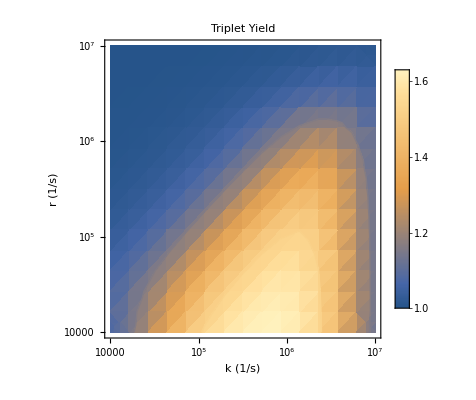

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;DensityPlot[Abs[((SingletBornTripletYield[nA,spinA,hfcA,nB,spinB,hfcB,0.05526*γe,k,0,0,r])/(SingletBornTripletYield[nA,spinA,hfcA,nB,spi,hfcB,0.00029 *γe,k,0,0,r]))],{k,1.0* 10^4,1.0* 10^7},{r,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->{{1.16,1.52}}, MeshStyle->Thick,FrameLabel ->{"k  (1/s)","r (1/s)"}, PlotLabel ->"Triplet Yield",LabelStyle -> Directive[ Bold]]
```

## Figure 4

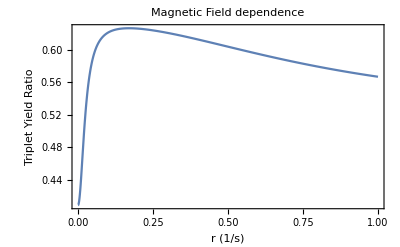

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;Plot[SingletBornTripletYield[nA,spinA,hfcA,nB,spinB,hfcB,B0*γe,2.0* 10^6,0,0,2.0*10^5],{B0,0.0,1.0},PlotLabel ->"Magnetic Field dependence", FrameLabel ->{"r  (1/s)","Triplet Yield Ratio" },Frame->True,LabelStyle -> Directive[ Bold],PlotRange->All]
```

## Figure 5

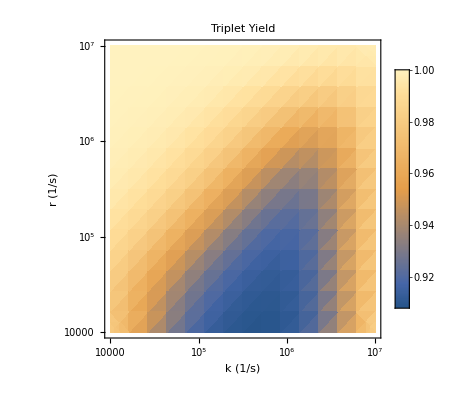

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;DensityPlot[Abs[((TripletBornTripletYield[nA,spinA,hfcA,nB,spinB,hfcB,0.05526*γe,k,0,0,r])/(TripletBornTripletYield[nA,spinA,hfcA,nB,spi,hfcB,0.00029 *γe,k,0,0,r]))],{k,1.0* 10^4,1.0* 10^7},{r,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->{{1.16}}, FrameLabel ->{"k  (1/s)","r (1/s)"}, PlotLabel ->"Triplet Yield",LabelStyle -> Directive[ Bold]]
```

## Figure 6

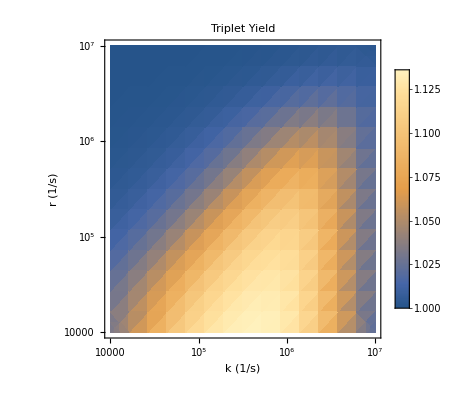

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;spinB={6};
hfcB={({{1886.8, 0, 0}, {0, 1886.8, 0}, {0, 0, 1886.8}})}γe;
nB=1;DensityPlot[Abs[((SingletBornTripletYield[nA,spinA,hfcA,nB,spinB,hfcB,0.05526*γe,k,0,0,r])/(SingletBornTripletYield[nA,spinA,hfcA,nB,spinB,hfcB,0.00029 *γe,k,0,0,r]))],{k,1.0* 10^4,1.0* 10^7},{r,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->{{1.16,1.52}}, MeshStyle->Thick,FrameLabel ->{"k  (1/s)","r (1/s)"}, PlotLabel ->"Triplet Yield",LabelStyle -> Directive[ Bold]]
```